The following code is part of Natasha Dada’s Wolfram Summer School 2018 project, An Analysis of Word Choice in the Real Estate Industry. This code identifies the most frequently used words and their success in a collection of MLS house listings from the Boston area from April-June 2018.

A list of house listings, each in the form {house description (string), percent difference between listing and selling price of the house (number)}:

```mathematica
data = Get["data.mx"];
```

The house descriptions without stopwords or numerical values:

```mathematica
tokenizedData = Transpose[{Select[TextWords@ToLowerCase@DeleteStopwords@First[#],!StringContainsQ[#,{"0","1","2","3","4","5","6","7","8","9"}]&]&/@data,data[[All,2]]}];
```

A neural net from the Wolfram Neural Net Repository for feature extraction of words:

```mathematica
glove=
NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"];
```

A list of words from every listing in the form {word, score of listing}:

```mathematica
allWords = Flatten[Transpose[{First[#],Table[Last[#],Length[First[#]]]}]&/@tokenizedData,1];
```

A list of words that occur in more than 1% of listings, scored according to the average success of the listings in which a word was used:

```mathematica
mostFrequentWords = Select[GatherBy[allWords,First],Length[#]>30&]; mostFrequentWords=SortBy[{First[First[#]],Mean[Last/@#]}&/@mostFrequentWords,Last];
```

A list of frequent words whose listing has a negative score:

```mathematica
negativeWords=Select[mostFrequentWords,Last[#]<0&];
```

Negative scores rescaled between 0 and 0.5 which will correspond to different shades of red:

```mathematica
rescaledNegativeScores = Rescale[negativeWords[[All,2]],MinMax[negativeWords[[All,2]]],{0,0.5}];
```

A list of frequent words whose listing has a positive score:

```mathematica
positiveWords=Select[mostFrequentWords,Last[#]>0&];
```

Positive scores rescaled between 0.5 and 1 which will correspond to different shades of green:

```mathematica
rescaledPositiveScores = Rescale[positiveWords[[All,2]],MinMax[positiveWords[[All,2]]],{0.5,1}];
```

The scores of all the most frequent words rescaled to values between 0 and 1:

```mathematica
rescaledScores = Join[rescaledNegativeScores,rescaledPositiveScores];
```

A list of each top word in the form {word, rescaled score}:

```mathematica
rescaledWords = Transpose[{mostFrequentWords[[All,1]],rescaledScores}];
```

A feature space plot that used a neural net to map each word. The color of each word corresponds to its success:

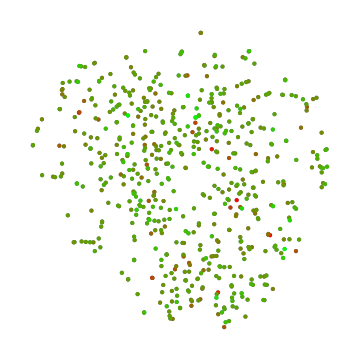

```mathematica
FeatureSpacePlot[Style[First[#],RGBColor[1-Last[#],Last[#],0]]&/@rescaledWords,FeatureExtractor->glove,LabelingFunction->Tooltip,ImageSize->Medium,PlotStyle->Directive[PointSize[Medium]]]
```

The words that were unsuccessful in order from most unsuccessful to least unsuccessful (worst to best):

```mathematica
mostNegativeWords = First/@Select[mostFrequentWords,Last[#]< -1&]
```

{wharf,residents,services,hour,valet,fireplaces,harbor,residential,service,month,concierge,interior,converted,years,beacon,lot,sf,west,lounge,club}

The words that were successful in order from least successful to most successful (worst to best):

```mathematica
mostPositiveWords=First/@Select[mostFrequentWords,Last[#]> 1&];
```

Some of the most successful words from least successful to most successful:

```mathematica
mostPositiveWords[[325;;388]]
```

{sun-filled,stained,tile,doors,front,seating,gem,white,urban,wonderful,sale,welcome,best,wide,summer,green,multiple,in-unit,move,sunday,stove,cambridge,recessed,backsplash,exposure,abundant,savin,landscaped,tree-lined,right,rear,lines,nestled,porch,fenced,dishwasher,fantastic,truly,off-street,siena,leading,due,love,saturday,fabulous,sink,stylish,seller,charming,value,fenway,showings,pm,oasis,monument,nursery,monday,april,houses,march,mantel,tuesday,directly,copley}

A selection of some of the most influential words:

```mathematica
wordCloudWords = Join[mostNegativeWords,mostPositiveWords[[325;;388]]];
```

Each word and a weight that will be used to size the word in a word cloud:

```mathematica
negativeAssoc= AssociationThread[mostNegativeWords,Reverse[Range[3,60,3]]];positiveAssoc=AssociationThread[mostPositiveWords[[325;;388]],Range[64]];
weights=Join[Values[negativeAssoc],Values[positiveAssoc]];
wordToWeight=AssociationThread[wordCloudWords,weights];
```

The color of each word in the word cloud, red for negative words and green for positive words:

```mathematica
colors = Join[Table[Red,Length[mostNegativeWords]],Table[Green,Length[mostPositiveWords[[325;;388]]]]];
wordToColor = AssociationThread[wordCloudWords,colors];
```

A word cloud of some of the most frequent words and their relative success. Unsuccessful words are shown in red and successful words in green. The larger the word, the greater its impact:

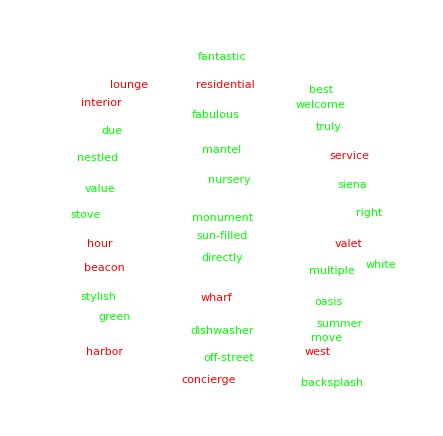

```mathematica
WordCloud[{Style[#,wordToColor[#]],wordToWeight[#]}&/@allWords]
```